### Predicting board game ratings: Getting my feet wet in Kaggle competitions

#### Background

I’ve never competed in a Kaggle competition (and still technically haven’t at the time of writing this), but I recently watched a video on YouTube of someone walking through building various models in R with a given dataset (link) and thought it would be interesting to try my hand at building some comparable models in Wolfram Language without submitting to Kaggle just yet.

The dataset and competition is based on trying to predict board game ratings using a number of inputs such as average playing time, number of players, and age range. The dataset can be found here. At the time of writing this post, here was the current leader board for the competition where the score is calculated from the root mean square.

-Graphics-

#### Load and organize the data

Load my personal library which contains numerous helper functions I use pretty often

```mathematica
Get["Alex`"];
```

Grab the data and do some quick cleaning

```mathematica
train=Import[FileNameJoin[{NotebookDirectory[],"train.csv"}]]//
	Function[associationThreadAll[First[#],Rest[#]]]//
	ReplaceAll["NA":>Missing[]];
	
test=Import[FileNameJoin[{NotebookDirectory[],"test.csv"}]]//
	Function[associationThreadAll[First[#],Rest[#]]]//
	ReplaceAll["NA":>Missing[]];
```

#### Initial EDA

What do the various histograms of the numerical data look like. For now, I’m going to ignore the string variables like mechanic, categories, and designer

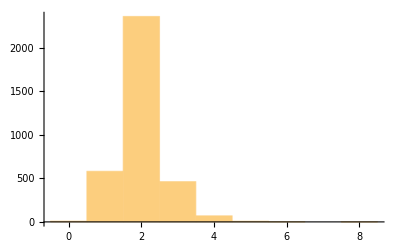
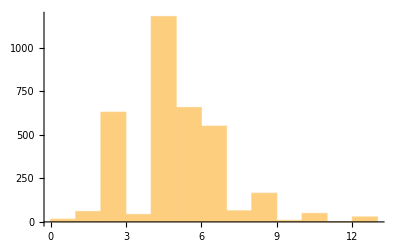
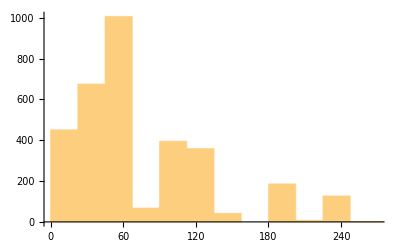
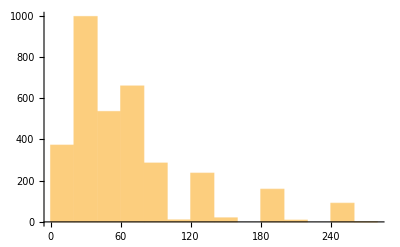
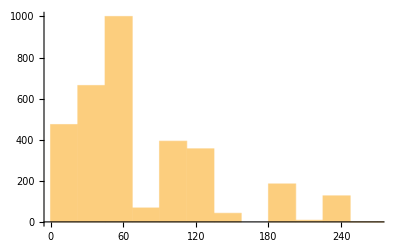
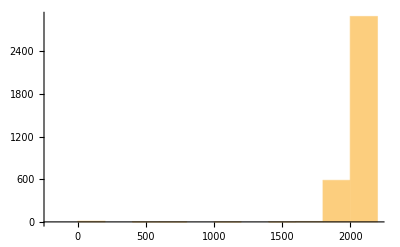
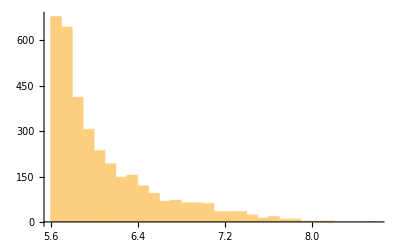
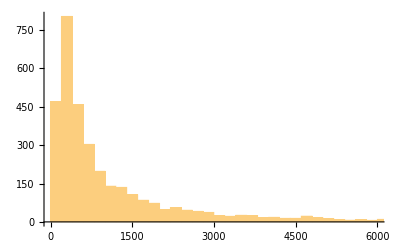
<|min_players→-Graphics-,max_players→-Graphics-,avg_time→-Graphics-,min_time→-Graphics-,max_time→-Graphics-,year→-Graphics-,geek_rating→-Graphics-,num_votes→-Graphics-,age→-Graphics-,owned→-Graphics-|>

```mathematica
Histogram/@Transpose[train,AllowedHeads->All][[{"min_players","max_players","avg_time","min_time","max_time","year","geek_rating","num_votes","age","owned"}]]
```

Similarly, for the numerical data, which ones appear to be more strongly correlated with ‘geek_rating’. From the looks of it, ‘num_votes’, ‘owned’, and ‘year’ all have positive correlations with the votes. Others like ‘max_players’, ‘min_time’, and ‘age’ seem to increase then peak before ultimately decreasing

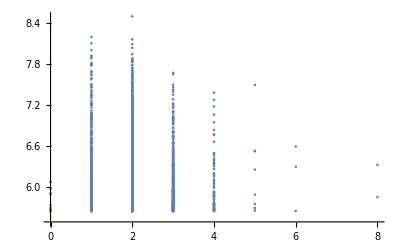
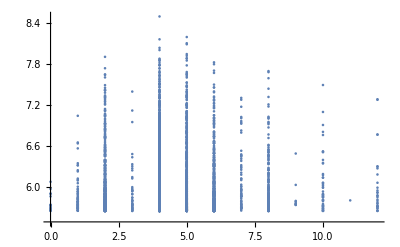
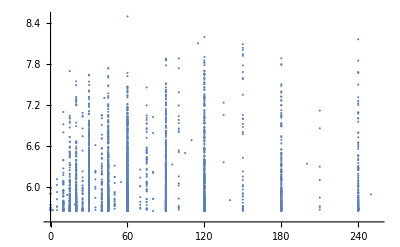
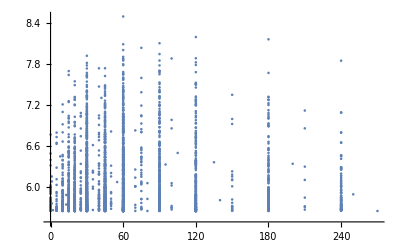
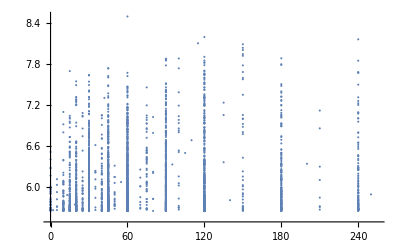
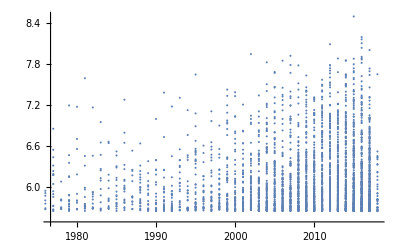
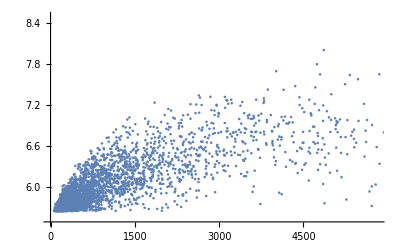
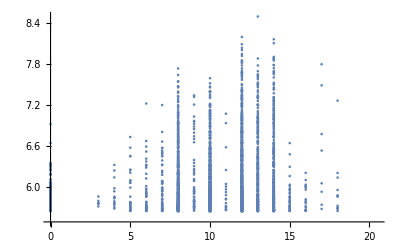
<|min_players→-Graphics-,max_players→-Graphics-,avg_time→-Graphics-,min_time→-Graphics-,max_time→-Graphics-,year→-Graphics-,num_votes→-Graphics-,age→-Graphics-,owned→-Graphics-|>

```mathematica
Association@Table[key->ListPlot[Values@train[[All,{key,"geek_rating"}]],PlotRange->Automatic],{key,{"min_players","max_players","avg_time","min_time","max_time","year","num_votes","age","owned"}}]
```

It looks like there’s potentially a logarithmic relationship for ‘num_votes’ and ‘owned’, so let’s check those a little closer

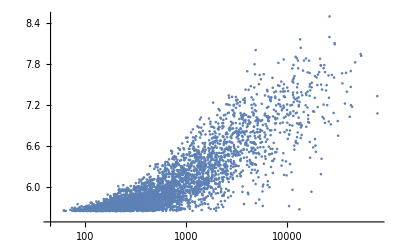

```mathematica
ListLogLinearPlot[Values@train[[All,{"num_votes","geek_rating"}]]]
```

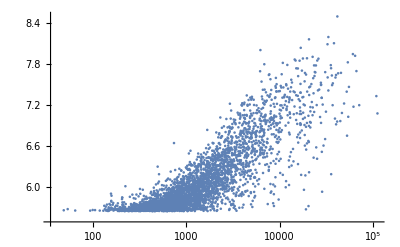

```mathematica
ListLogLinearPlot[Values@train[[All,{"owned","geek_rating"}]]]
```

#### Linear modeling

Following the original video, I’ll start first with a linear model and slowly add terms just to see how much it reduces my root mean square (RMS).

Note, as mentioned in the video, if we just take an average value from the ‘geek_ratings’, the standard deviation will give you the RMS.

```mathematica
train[[All,"geek_rating"]]//StandardDeviation
```

0.482988

Adding a linear model using just ‘owned’

```mathematica
fit=LinearModelFit[Values[train[[All,{"owned","geek_rating"}]]],x,x]
```

FittedModel[5.93963+0.0000484429 x]

```mathematica
RootMeanSquare[Map[fit]@train[[All,"owned"]]-train[[All,"geek_rating"]]]
```

0.371532

By using a Log transform with base 2 and offset 1 with just owned data gets us to 0.267

```mathematica
fit=LinearModelFit[MapAt[Function[Log[2,#+1]],Values[train[[All,{"owned","geek_rating"}]]],{All,1}],x,x]
```

FittedModel[3.50462+0.247265 x]

```mathematica
RootMeanSquare[Map[fit]@Map[Function[Log[2,#+1]]]@train[[All,"owned"]]-train[[All,"geek_rating"]]]
```

0.267536